Answer for 6(a)

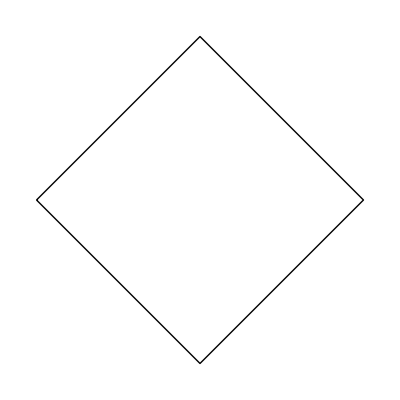

```mathematica
Graphics[Line[{{0,0},{1,1},{2,0},{1,-1},{0,0}}]]
```

```mathematica
Solve[{u== x-y,v == x+y},{x,y}]
```

{{x→(u+v)/2,y→1/2 (-u+v)}}

```mathematica
x = (u+v)/2;
```

```mathematica
y = 1/2 (-u+v);
```

```mathematica
(0,0),(1,1),(2,0),(1,-1)
```

```mathematica
Simplify[Solve[(y - y1)/(x - x1)  == (y2 - y1)/(x2 - x1),v]/.{x1 -> 0,y1-> 0,x2 -> 1, y2 ->- 1}]
```

{{v→0}}

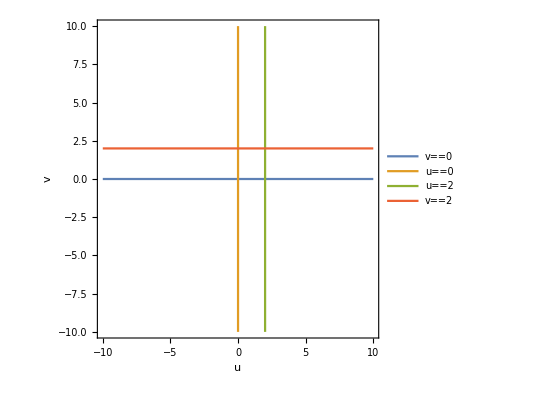

```mathematica
plot = ContourPlot[{  v ==  0, u == 0 , u == 2, v == 2},{u,-10,10},{v,-10,10},Axes -> True , AxesLabel-> Automatic , PlotLegends->"Expressions"]
```

Answer for 6(b)

```mathematica
jac = Det[D[{x,y},{{u,v}}]]
```

1/2

Answer for 6(c)

```mathematica
∫_0^2 ∫_0^2 x y(jac)ⅆvⅆu
```

0